First we need a way to plot vectors:

```mathematica
PlotVector[l_]:=Graphics[Arrow[{{0,0},#}]&/@l,PlotRange->{{-2,2},{-2,2}},
Axes->True];
```

Initialize rotational matrices:

```mathematica
mRight=RotationMatrix[π/2];
mLeft=RotationMatrix[-π/2];
mBelow=RotationMatrix[π];
mTop=RotationMatrix[0];
Grid[{MatrixForm/@{mRight,mLeft,mBelow,mTop}},Frame->All]
```

(0 | -1
1 | 0) | (0 | 1
-1 | 0) | (-1 | 0
0 | -1) | (1 | 0
0 | 1)

Slightly unaligned version:

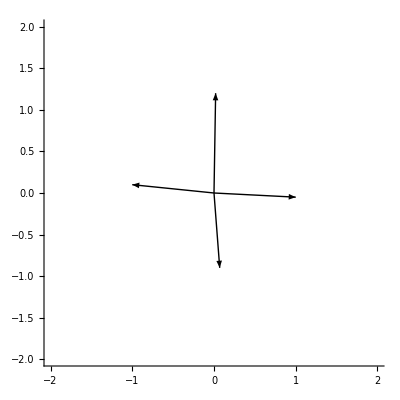

```mathematica
right={1,-0.05};
top={0.02,1.2};
left={-1,0.1};
below={0.07,-0.9};
PlotVector[{top,right,left,below}]
```

```mathematica
getTransform[right_,front_,left_,back_]:=
{
Normalize[right-left],
Normalize[front-back]
}
```

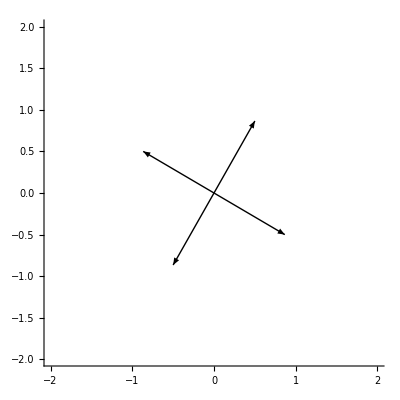

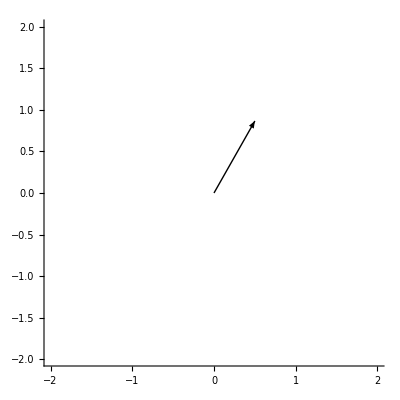
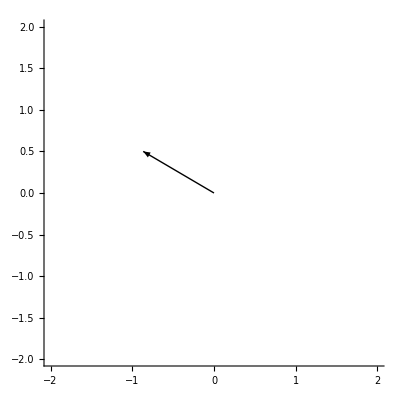
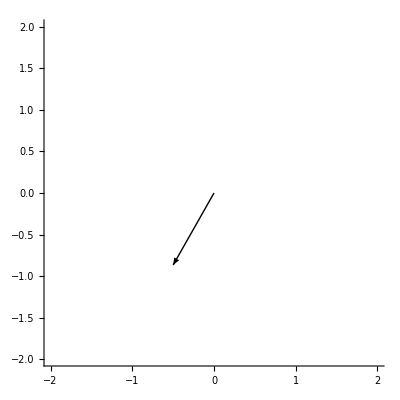
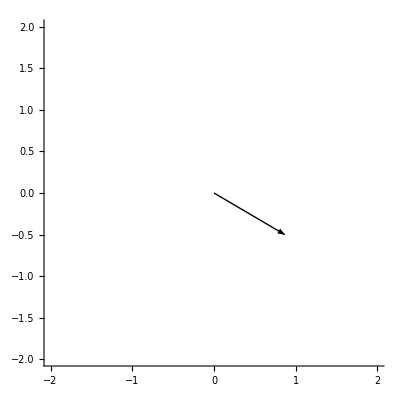

```mathematica
{rotRight,rotFront,rotLeft,rotBack}=RotationMatrix[π/3].#&/@{
{1,0},{0,1},{-1,0},{0,-1}
};
PlotVector[{rotRight,rotFront,rotLeft,rotBack}]
PlotVector[{#}]&/@{rotRight,rotFront,rotLeft,rotBack}
```

(1/2 | (√3)/2
-(√3)/2 | 1/2)

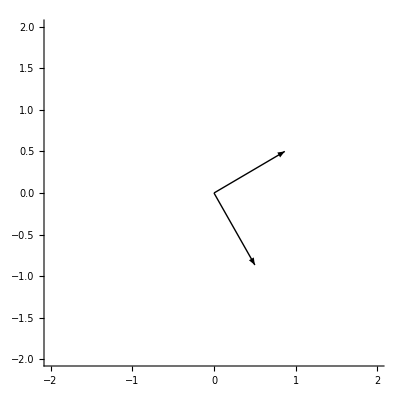

```mathematica
M=getTransform[rotRight,rotFront,rotLeft,rotBack];
M//MatrixForm
PlotVector[M//Transpose]
```

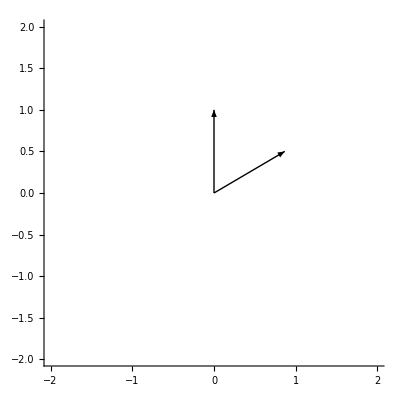

```mathematica
PlotVector[{
{0,1},
M.{0,1}
}]
```

Rotate the neighbor directions to all point forward:

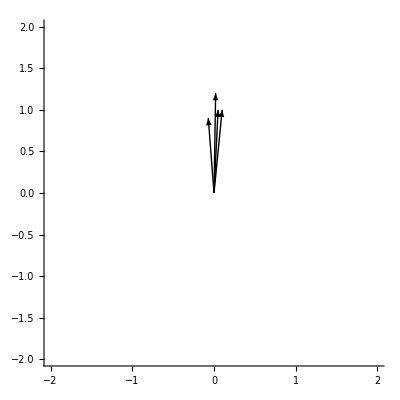

```mathematica
PlotVector[{
mTop.top,
mRight.right,
mLeft.left,
mBelow.below
}]
```

And take the mean direction:

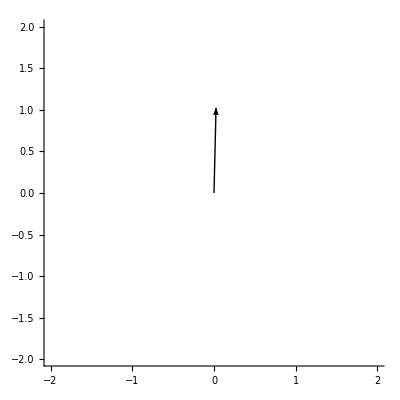

```mathematica
PlotVector[
{(mTop.top+mRight.right+mLeft.left+mBelow.below)/4}
]
```

Rotate a little more to see if it still works:

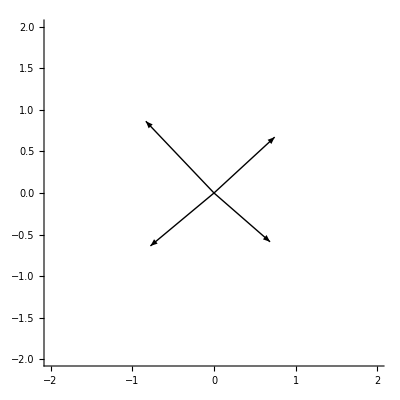

```mathematica
{rotTop,rotLeft,rotRight,rotBelow}=RotationMatrix[π/4].#&/@{top,left,right,below};
PlotVector[{rotTop,rotLeft,rotRight,rotBelow}]
```

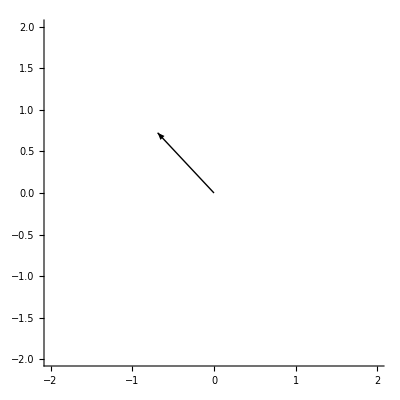

```mathematica
PlotVector[
{(mTop.rotTop+mRight.rotRight+mLeft.rotLeft+mBelow.rotBelow)//Normalize}
]
```

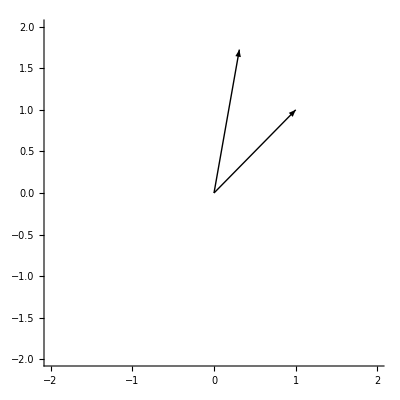

```mathematica
With[{v={1,1}},PlotVector[{
v,
Normalize[mTop.rotTop+mRight.rotRight+mLeft.rotLeft+mBelow.rotBelow]+v
}]]
```

```mathematica
Rot2[a_,b_]:=Module[{},
base=]
```

```mathematica
Rot[a_,b_]:=Module[{v,s,c,vx,I},
v=a×b;
s=Norm[v];
Print[v];
Print[s];
c=a.b;
Print[c];
vx = ({{0, -v⟦3⟧, v⟦2⟧}, {v⟦3⟧, 0, -v⟦1⟧}, {-v⟦2⟧, v⟦1⟧, 0}});
I=IdentityMatrix[3];
I+vx+vx^2 1/(1+c)
]
```

```mathematica
Rot[{1,1,0},{2,-1,0}]
```

{0,0,-3}

3

1

{{1,15/2,0},{3/2,1,0},{0,0,1}}